# Optimization of the time-averaged excess work in STIRAP

## Parameters and definitions

```mathematica
ℏ = 1
ti = 0
Δ= 0.1
(*Boundary conditions for the protocols*)
Ωpi = 10.0
Ωpf = 0.1
(*Range of the protocol time*)
Tmin = 0.1
Tmax = 30.1
(*Sample size*)
m = 9
ΔT = (Tmax-Tmin)/m
(*Protocols*)
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
(*Initial conditions - |n0 >*)
(*c10 = Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]
c20 = 0
c30 = -Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]*)
(*Initial conditions - |n- >*)
ϕ0 = 0.5*ArcTan[Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ]/Δ]
c10 = (Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ0]
c20 = -Sin[ϕ0]
c30 = (Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ])*Cos[ϕ0]
(*Final state in adiabatic evolution*)
ϕf = 0.5*ArcTan[Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ]/Δ]
c1f = (Ωp[tf,tf]/Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ])*Cos[ϕf]
c2f = -Sin[ϕf]
c3f = (Ωs[tf]/Sqrt[Ωs[tf]^2 + Ωp[tf,tf]^2 ])*Cos[ϕf]
(*Counterdiabatic driving for the linear protocol*)
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
(*Energetic costs*)
Cost[Ωp_,Ωs_,Ωa_,Δ_,tf_] := NIntegrate[√(Δ^2 ℏ^2+(Ωa^2 ℏ^2)/2+(Ωp^2 ℏ^2)/2+(Ωs^2 ℏ^2)/2),{t,ti,tf}]/tf
Wex[c1_,c2_,c3_,Ωp_,Ωs_,Δ_] := ℏ*(Ωp*Re[c1*Conjugate[c2]] + Ωs*Re[c2*Conjugate[c3]]+ 2*Δ*Abs[c2]^2)
(*Sample points*)
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

1

0

0.1

10.

0.1

0.1

30.1

9

3.33333

0.780423

0.707089

-0.70358

0.0707089

0.73581

0.0737609

-0.671187

0.737609

{0.0454959,1.56203,3.07856,4.59509,6.11162,7.62815,9.14468,10.6612,12.1777,13.6943}

```mathematica
(*Minimum fidelity*)
Fmin = Abs[c10*c1f + c20*c2f + c30*c3f]
```

0.576545

## Linear protocol

The linear protocol and the variation of the eigenvalues

1.

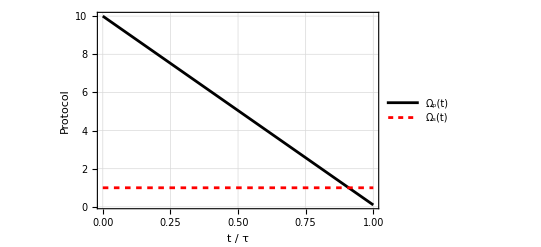

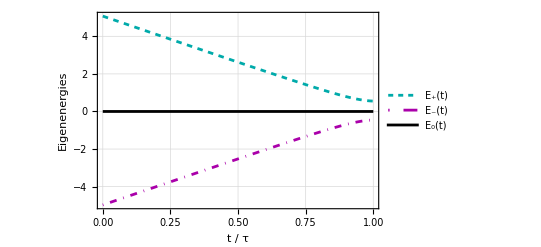

-Graphics-

```mathematica
tf = 1.0
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], Dashing[0.01]},FrameLabel ->{"t / τ", "Eigenenergies"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Magenta], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.78}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Black],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.86}]]]
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

Solution of the Schrödinger equation for the linear protocol

```mathematica
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==c10,c2[ti]==c20,c3[ti]==c30 },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

```mathematica
(*Fidelity*)
FLIN = Table[Abs[(c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
```

{0.57699,0.694997,0.757162,0.795823,0.825816,0.850383,0.869089,0.885121,0.898852,0.90986}

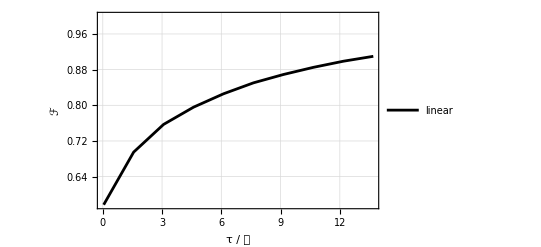

```mathematica
(*Population transfer*)
gLIN = ListPlot[Transpose[{time,FLIN}], Joined->True,PlotStyle->{Black}, PlotRange->{Fmin,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "ℱ"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.10}]]
```

## Minimal action

The protocols of the minimal action (MA) method comes from the minimization of the adiabatic action.

```mathematica
(*Transitions between n- and n0*)
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
(*Transitions between n- and n+*)
ProtMA3 = Table[NDSolve[{D[ΩpMA3'[t]/(ΩpMA3[t]^2 + Ωs[t]^2),t] ==0 , ΩpMA3[ti]==Ωpi, ΩpMA3[tf]==Ωpf},ΩpMA3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

{{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}},{{ΩpMA3→InterpolatingFunction[…]}}}

5

13.4333

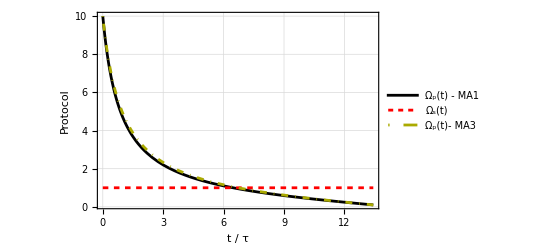

```mathematica
(*Protocol time for the Figure*)
n = 5
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - MA1",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.78}]],Plot[Evaluate[ΩpMA3[t]/.Flatten[Part[ProtMA3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Yellow], DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)- MA3",10]},LegendLayout->"Row"],{Right,0.86}]]]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==c10,c2MA[ti]==c20,c3MA[ti]==c30 },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

```mathematica
(*Fidelity*)
FLIN = Table[Abs[(c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]/.t->tf)*c1f +(c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]/.t->tf)*c2f + (c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]/.t->tf)*c3f  ] ,{tf,Tmin,Tmax,ΔT}]
```

## Fast quasidiabatic

The protocols for the fast quasidiabatic method (FQ) can be found by solving the EDO generated when we make the adiabatic quantitative condition constant.

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
ProtFQ2 = Table[NDSolve[{D[ΩpFQ2'[t]/(ΩpFQ2[t]^2 + Ωs[t]^2)^(3/2)*(1-1.5*Δ/(ΩpFQ2[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ2[ti]==Ωpi, ΩpFQ2[tf]==Ωpf},ΩpFQ2,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
ProtFQ3 = Table[DSolve[{D[ΩpFQ3[t]*ΩpFQ3'[t]/(ΩpFQ3[t]^2 + Ωs[t]^2)^(4/2),t] ==0 , ΩpFQ3[ti]==Ωpi, ΩpFQ3[tf]==Ωpf},ΩpFQ3,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

{{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}},{{ΩpFQ2→InterpolatingFunction[…]}}}

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

General::stop: Further output of DSolve::bvnul will be suppressed during this calculation.

{{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+9.80198 t)/(0.49505-4.90099 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.173657 t)/(0.49505-0.0868286 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0876046 t)/(0.49505-0.0438023 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0585776 t)/(0.49505-0.0292888 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0439989 t)/(0.49505-0.0219995 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0352308 t)/(0.49505-0.0176154 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0293766 t)/(0.49505-0.0146883 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0251907 t)/(0.49505-0.0125953 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.0220489 t)/(0.49505-0.0110245 t))]}},{{ΩpFQ3→Function[{t},0.707107 √((0.00990099+0.019604 t)/(0.49505-0.00980198 t))]}}}

Protocols for the fast quasidiabatic method.

1

0.1

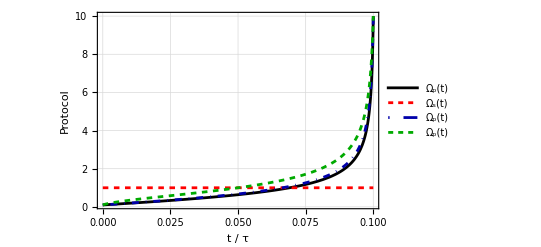

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.72}]],Plot[Evaluate[ΩpFQ2[t]/.Flatten[Part[ProtFQ2, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Blue],DotDashed},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.86}]],Plot[Evaluate[ΩpFQ3[t]/.Flatten[Part[ProtFQ3, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Green],Dashing[0.01]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.78}]]]
```

Solution of the Schrödinger equation for the fast quasidiabatic protocol.

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==c10,c2FQ[ti]==c20,c3FQ[ti]==c30 },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

```mathematica
(*Population transfer*)
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexFQ = Table[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexFQtimeaveraged= Table[NIntegrate[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1],c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2],c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CFQ = Table[Cost[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.0359962,0.0447439,0.0106516,0.00961527,0.0153444,0.00834906,0.0151417,0.00773029,0.00860836}

{0.00187438,0.146895,0.0654347,0.00742654,0.0125174,0.00648906,0.00659016,0.00280291,0.000953244,0.00489469}

{0.00999996,0.817108,0.889821,0.981922,0.977867,0.978166,0.985061,0.982055,0.991316,0.986497}

{-0.000602043,-0.3779,0.0504174,0.0117853,-0.0678195,0.0281024,0.000198183,-0.0220817,0.00970121,-0.00200368}

{-3.36497×10^-6,-0.0122677,-0.000760596,-0.00230784,-0.000591812,-0.000279874,-0.000517296,-0.000201298,-0.000156836,-0.000183686}

{1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

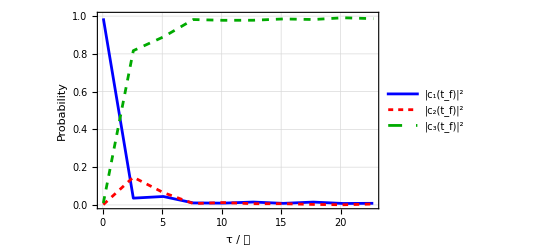

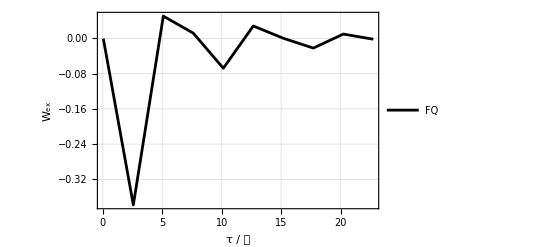

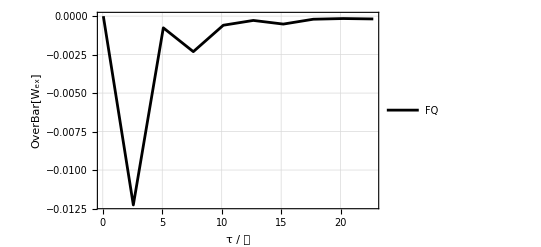

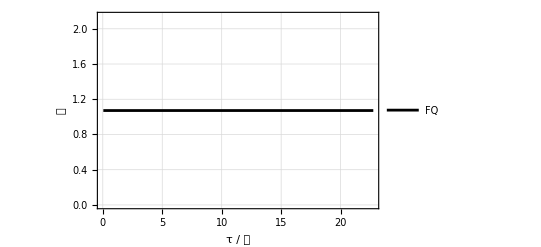

```mathematica
(*Population transfer*)
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Excess work*)
 gWexFQ = ListPlot[Transpose[{time,WexFQ}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time-averaged excess work*)
 gWexFQtimeaveraged = ListPlot[Transpose[{time,WexFQtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCFQ = ListPlot[Transpose[{time,CFQ}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Optimal time-averaged excess work

Apparently, the protocol found by optimizing the time-averaged excess work is equal to de fast quasidiabatic protocol. The protocols can be found by using the Euler-Lagrange equations on the excess work. The solutions are given below.

```mathematica
ProtOP = Table[NDSolve[{(1+ΩpOP[t]^2) (1+3 ΩpOP[t]^2+3 ΩpOP[t]^4+ΩpOP[t]^6-12 ΩpOP'[t]^2) (-3 ΩpOP[t] ΩpOP'[t]^2+ΩpOP''[t]+ΩpOP[t]^2 ΩpOP''[t])==0, ΩpOP[ti]==Ωpi, ΩpOP[tf]==Ωpf},ΩpOP[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}}}

Protocol found by minimizing the time-averaged excess work.

1

0.1

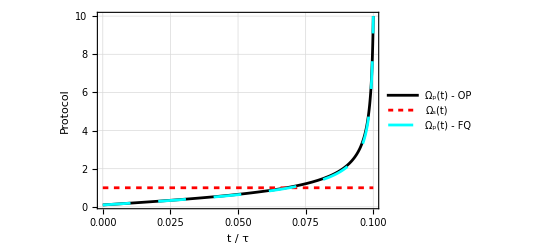

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpOP[t]/.Flatten[Part[ProtOP, n]]],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - OP",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti, Tmin + (n-1)*ΔT},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Cyan, Dashing[0.05]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ",10]},LegendLayout->"Row"],{Left,0.86}]]]
```